```mathematica
list=RandomInteger[{0,1},20]
```

{0,0,0,0,1,0,0,1,0,0,0,1,1,0,1,0,1,0,0,1}

```mathematica
ToString[list]
```

{0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 1, 1, 0, 1, 0, 1, 0, 0, 1}

```mathematica
StringLength@ExportString[list,"GZIP"]
```

36

```mathematica
ExportString[Table[1,{20}],"GZIP"]
```

.1f.8b.08.00.00.00.00.00.00.13«6ÔQ .13Õ.02.00.9a${"<.00.00.00

```mathematica
ToCharacterCode[ExportString[Table[1,{20}],"GZIP"]]
```

{31,139,8,0,0,0,0,0,0,19,171,54,212,81,32,19,213,2,0,154,36,123,34,60,0,0,0}

```mathematica
data=StringLength@ExportString[#,"GZIP"]&/@CellularAutomaton[110,RandomInteger[{0,1},500],2000];
```

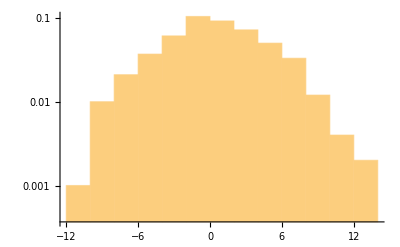

```mathematica
Histogram[Differences[data⟦1;;500⟧],Automatic,{"Log","PDF"}]
```

```mathematica
p=Count[Differences[data⟦1;;500⟧],x_/;x>0]/500
```

11/25

```mathematica
N@Log[1/p]
```

0.820981

```mathematica
Clear[p]
```

```mathematica
T[da_]:=Module[{dE=-Mean[Differences[da]],p=1/Length[da] Count[Differences[da],x_/;x>0]},
-dE/Log[2 (p+0.001)]
]
```

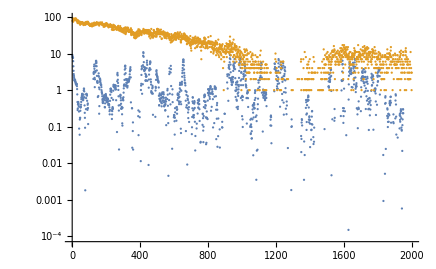

```mathematica
ListPlot[{GaussianFilter[MovingMap[T,data,50],3],data-80},ScalingFunctions->"Log"]
```

```mathematica
t54=GaussianFilter[MovingMap[T,data,50],1];
```

```mathematica
t110=GaussianFilter[MovingMap[T,data,50],1];
```

```mathematica
t90=GaussianFilter[MovingMap[T,data,50],1];
```

```mathematica
t30=GaussianFilter[MovingMap[T,data,50],1];
```

```mathematica
t54=Select[t54,#>0&];
t110=Select[t110,#>0&];
t90=Select[t90,#>0&];
t30=Select[t30,#>0&];
```

```mathematica
StandardDeviation/@{t54,t110,t90,t30}
```

{2.07291,1.47584,1.35567,1.14209}

```mathematica
Mean/@{t54,t110,t90,t30}
```

{1.36879,1.13444,0.904333,0.692796}

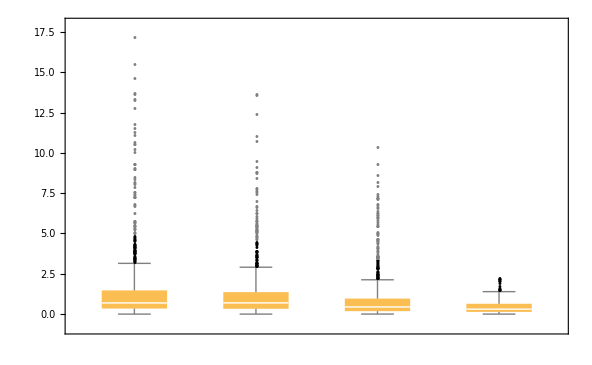

```mathematica
BoxWhiskerChart[{t54,t110,t90,t30},"Outliers"]
```

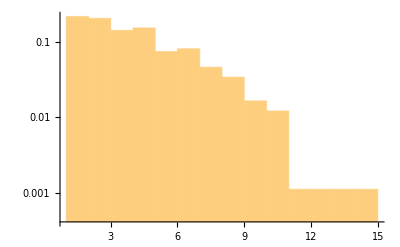

```mathematica
Histogram[Select[Differences[data],#>0&],Automatic,{"Log","PDF"}]
```

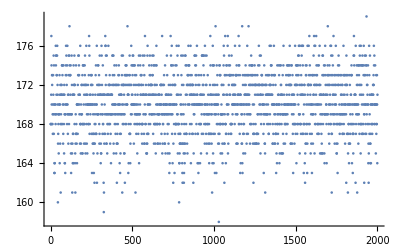

```mathematica
ListPlot[data]
```

```mathematica
Solve[1/2 ⅇ^(-β dE)==p,β]
```

{{β→ConditionalExpression[(2 ⅈ π C[1]+Log[1/(2 p)])/dE,C[1]∈Integers]}}